FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

L

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.451024-0.270615 ⅇ^(-0.7-0.5 (1.-1. em2)-0.5 em2)-0.196299 ⅇ^(0.5 em2)+0.0255463 ⅇ^(1. em2)-0.270615 em2-0.0508558 ⅇ^(«1») em2+0.270615 ⅇ^(-0.7-0.5 «1»-0.5 em2) em2+0.118663 ⅇ^(-0.5 (1.-1. em2)-0.5 em2) em2-0.229089 ⅇ^(-0.5 em2) em2+0.239409 ⅇ^(0.5 em2) em2+«162» encountered.

Infinity::indet: Indeterminate expression 1.45102-0.270615 ⅇ^(-0.7-0.5 (1.-1. em2)-0.5 em2)-0.340028 ⅇ^(0.5 em2)-0.270615 em2+0.270615 ⅇ^(-0.7-0.5 (1.-1. em2)-0.5 em2) em2-0.466059 ⅇ^(-0.5 em2) em2+0.340028 ⅇ^(0.5 em2) em2+ComplexInfinity+ComplexInfinity+ComplexInfinity+«152» encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {em2} = {0.4}.

Infinity::indet: Indeterminate expression 0.451024-0.270615 ⅇ^(-0.7-0.5 (1.-1. em2)-0.5 em2)-0.196299 ⅇ^(0.5 em2)+0.0255463 ⅇ^(1. em2)-0.270615 em2-0.0508558 ⅇ^(«1») em2+0.270615 ⅇ^(-0.7-0.5 «1»-0.5 em2) em2+0.118663 ⅇ^(-0.5 (1.-1. em2)-0.5 em2) em2-0.229089 ⅇ^(-0.5 em2) em2+0.239409 ⅇ^(0.5 em2) em2+«162» encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {em2} = {0.4}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{res23==0},{em2,0.4,0.6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.451024-0.270615 ⅇ^(-0.7-0.5 (1.-1. em2)-0.5 em2)-0.196299 ⅇ^(0.5 em2)+0.0255463 ⅇ^(1. em2)-0.270615 em2-0.0508558 ⅇ^(«1») em2+0.270615 ⅇ^(-0.7-0.5 «1»-0.5 em2) em2+0.118663 ⅇ^(-0.5 (1.-1. em2)-0.5 em2) em2-0.229089 ⅇ^(-0.5 em2) em2+0.239409 ⅇ^(0.5 em2) em2+«162» encountered.

Infinity::indet: Indeterminate expression 1.45102-0.270615 ⅇ^(-0.7-0.5 (1.-1. em2)-0.5 em2)-0.340028 ⅇ^(0.5 em2)-0.270615 em2+0.270615 ⅇ^(-0.7-0.5 (1.-1. em2)-0.5 em2) em2-0.466059 ⅇ^(-0.5 em2) em2+0.340028 ⅇ^(0.5 em2) em2+ComplexInfinity+ComplexInfinity+ComplexInfinity+«152» encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {em2} = {0.4}.

ReplaceAll::reps: {FindRoot[{res23==0},{em2,0.4,0.6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Infinity::indet: Indeterminate expression 0.451024-0.270615 ⅇ^(-0.7-0.5 (1.-1. em2)-0.5 em2)-0.196299 ⅇ^(0.5 em2)+0.0255463 ⅇ^(1. em2)-0.270615 em2-0.0508558 ⅇ^(«1») em2+0.270615 ⅇ^(-0.7-0.5 «1»-0.5 em2) em2+0.118663 ⅇ^(-0.5 (1.-1. em2)-0.5 em2) em2-0.229089 ⅇ^(-0.5 em2) em2+0.239409 ⅇ^(0.5 em2) em2+«162» encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {em2} = {0.4}.

ReplaceAll::reps: {FindRoot[{res23==0},{em2,0.4,0.6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {em2} = {0.4}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{res23==0},{em2,0.4,0.6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

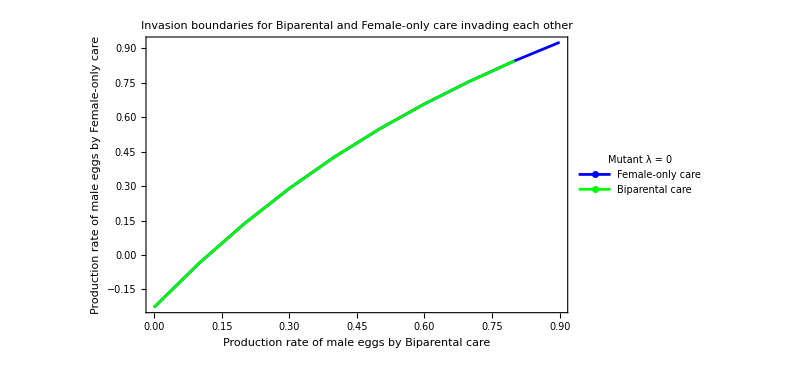

```mathematica
(*16th Jan 2024, defining trade-offs and parameter values outside of the params1 function*)

(*BASELINES*)
em0=0.5;
ef0 = 1-em0;
(*Now using numbers from literature justifications*)
mum0=0.5;
muf0= 0.5;

sigjm0=0.6;
sigjf0=0.6;
taum0=0.1;
tauf0=0.1;

mm0=0.5;
mf0=0.5;

k0=250;
rr0=6;
wm0=0.4;
wf0=0.4;

z0=1;
(*_________________________________________________________________________*)
(*RESIDENTS*)


(*Male only care*)

(*emres=em0;*)
efres =1-emres;

zres = z0;
cmres = 0.7;
cfres = 0.0;
ctres = cmres+cfres;

mumres=mum0*E^(-zres*ctres);
mufres=muf0*E^(-zres*ctres);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;

mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
wmres=1-((1-wm0)*E^(-cmres));
wfres= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres)));

KR=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

emmres = emres*(1-mumres)*mmres;
emfres = efres* (1-mufres)*mfres;
esmres= emres*(1-mumres);
esfres = efres* (1-mufres);
amres = emres*(1-mumres)*mmres*sigjmres;
afres = efres* (1-mufres)* mfres*sigjfres;

AR =KR*(1-((wmres*amres+wfres*afres)*(mumres*emres + mufres*efres + mmres*esmres + mfres*esfres)/((emmres*sigjmres+emfres*sigjfres)*rres*afres)));




(*Female only*)
(*emres2=em0;*)
efres2 =1-emres2;

zres2 = z0;
cmres2 = 0.0;
cfres2 = 0.7;
ctres2 = cmres2+cfres2;

mumres2=mum0*E^(-zres2*ctres2);
mufres2=muf0*E^(-zres2*ctres2);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;

mmres2=1-((1-mm0)*E^(-((1-mum0)*emres2)));
mfres2=1-((1-mf0)*E^(-((1-muf0)*efres2)));
KR2=k0;
rres2=rr0*E^(-((1-mum0)*emres2+((1-muf0)*efres2))/2);

wmres2=1-((1-wm0)*E^(-cmres2));
wfres2= 1-((1-wf0)*E^(-(efres2*(1-muf0)+(1-mum0)*emres2+cfres2)));

emmres2 = emres2*(1-mumres2)*mmres2;
emfres2 = efres2* (1-mufres2)*mfres2;
esmres2= emres2*(1-mumres2);
esfres2 = efres2* (1-mufres2);
amres2 = emres2*(1-mumres2)*mmres2*sigjmres;
afres2 = efres2* (1-mufres2)* mfres2*sigjfres;

AR2 =KR2*(1-((wmres2*amres2+wfres2*afres2)*(mumres2*emres2 + mufres2*efres2 + mmres2*esmres2 + mfres2*esfres2)/((emmres2*sigjmres+emfres2*sigjfres)*rres2*afres2)));



(*Biparental*)
(*emres3=em0*)
efres3 =1-emres3;

zres3 = z0;
cmres3 = 0.35;
cfres3 = 0.35;
ctres3 = cmres3+cfres3;

mumres3=mum0*E^(-zres3*ctres3);
mufres3=muf0*E^(-zres*ctres3);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres3=1-((1-mm0)*E^(-((1-mum0)*emres3)));
mfres3=1-((1-mf0)*E^(-((1-muf0)*efres3)));
KR3=k0;
rres3=rr0*E^(-((1-mum0)*emres3+((1-muf0)*efres3))/2);

wmres3=1-((1-wm0)*E^(-cmres3));
wfres3= 1-((1-wf0)*E^(-(efres3*(1-muf0)+(1-mum0)*emres3+cfres3)));

emmres3 = emres3*(1-mumres3)*mmres3;
emfres3 = efres3* (1-mufres3)*mfres3;
esmres3= emres3*(1-mumres3);
esfres3 = efres3* (1-mufres3);
amres3 = emres3*(1-mumres3)*mmres3*sigjmres;
afres3 = efres3* (1-mufres3)* mfres3*sigjfres;

AR3 =KR3*(1-((wmres3*amres3+wfres3*afres3)*(mumres3*emres3 + mufres3*efres3 + mmres3*esmres3 + mfres3*esfres3)/((emmres3*sigjmres+emfres3*sigjfres)*rres3*afres3)));




(*No care*)

(*emres4=em0;*)
efres4 =1-emres4;

zres4 = z0;
cmres4 = 0.0;
cfres4 = 0.0;
ctres4 = cmres4+cfres4;

mumres4=mum0*E^(-zres4*ctres4);
mufres4=muf0*E^(-zres4*ctres4);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres4=1-((1-mm0)*E^(-((1-mum0)*emres4)));
mfres4=1-((1-mf0)*E^(-((1-muf0)*efres4)));

KR4=k0;
rres4=rr0*E^(-((1-mum0)*emres4+((1-muf0)*efres4))/2);

wmres4=1-((1-wm0)*E^(-cmres4));
wfres4= 1-((1-wf0)*E^(-(efres4*(1-muf0)+(1-mum0)*emres4+cfres4)));

emmres4 = emres4*(1-mumres4)*mmres4;
emfres4= efres4* (1-mufres4)*mfres4;
esmres4= emres4*(1-mumres4);
esfres4 = efres4* (1-mufres4);
amres4 = emres4*(1-mumres4)*mmres4*sigjmres;
afres4 = efres4* (1-mufres4)* mfres4*sigjfres;

AR4 =KR4*(1-((wmres4*amres4+wfres4*afres4)*(mumres4*emres4 + mufres4*efres4 + mmres4*esmres4 + mfres4*esfres4)/((emmres4*sigjmres+emfres4*sigjfres)*rres4*afres4)));
AR4;






(*___________________________________________________*)
(*MUTANTS*)

(*Male only care*)
z4=z0;
cm4=0.7;
cf4=0.0;
ct4 = cm4 + cf4;

mum4=mum0*E^(-z4*ct4);
muf4=muf0*E^(-z4*ct4);

(*em4=em0;*)
ef4 = 1-em4;
sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm4=1-((1-mm0)*E^(-((1-mum0)*em4)));
mf4=1-((1-mf0)*E^(-((1-muf0)*ef4)));
k4=k0; 
rr4=rr0*E^(-((1-mum0)*em4+((1-muf0)*ef4))/2);

wm4=1-((1-wm0)*E^(-cm4));
wf4=1-((1-wf0)*E^(-(ef4*(1-muf0)+(1-mum0)*em4 +cf4)));

emm4 = em4*(1-mum4)*mm4;
emf4 = ef4* (1-muf4)*mf4;
esm4= em4*(1-mum4);
esf4 = ef4*(1-muf4);
am4 = em4*(1-mum4)*mm4*sigjm;
af4= ef4* (1-muf4)* mf4*sigjf;

(*Female only care*)
z2=z0;
cm2=0.0;
cf2=0.7;
ct2 = cm2 + cf2;
ct2;
(*em2=em0;*)
ef2 = 1-em2;

mum2=mum0*E^(-z2*ct2);
muf2=muf0*E^(-z2*ct2);

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm2=1-((1-mm0)*E^(-((1-mum0)*em2)));
mf2=1-((1-mf0)*E^(-((1-muf0)*ef2)));

k=k0;
rr2=rr0*E^(-((1-mum0)*em2+((1-muf0)*ef2))/2);

wm2=1-((1-wm0)*E^(-cm2));
wf2=1-((1-wf0)*E^(-(ef2*(1-muf0)+(1-mum0)*em2 +cf2)));

emm2 = em2*(1-mum2)*mm2;
emf2 = ef2* (1-muf2)*mf2;
esm2 = em2*(1-mum2);
esf2 = ef2*(1-muf2);
am2 = em2*(1-mum2)*mm2*sigjm;
af2 = ef2* (1-muf2)* mf2*sigjf;


(*Biparental care*)
z3=z0;
cm3=0.35;
cf3=0.35;
ct3 = cm3 + cf3;
ct3;

(*em3=em0;*)
ef3=1-em3;

mum3=mum0*E^(-z3*ct3);
muf3=muf0*E^(-z3*ct3);

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm3=1-((1-mm0)*E^(-((1-mum0)*em3)));
mf3=1-((1-mf0)*E^(-((1-muf0)*ef3)));

wm3=1-((1-wm0)*E^(-cm3));
wf3=1-((1-wf0)*E^(-(ef3*(1-muf0)+(1-mum0)*em3 +cf3)));

emm3 = em3*(1-mum3)*mm3;
emf3 = ef3* (1-muf3)*mf3;
esm3 = em3*(1-mum3);
esf3 = ef3*(1-muf3);

k=k0;
rr3=rr0*E^(-((1-mum0)*em3+((1-muf0)*ef3))/2);

am3 = em3*(1-mum3)*mm3*sigjm;
af3 = ef3* (1-muf3)* mf3*sigjf;



(*No care*)

z=z0;
cm=0.0;
cf=0.0;
ct = cm + cf;

mum=mum0*E^(-z*ct);
muf=muf0*E^(-z*ct);

(*em=em0;*)
ef = 1-em;

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm=1-((1-mm0)*E^(-((1-mum0)*em)));
mf=1-((1-mf0)*E^(-((1-muf0)*ef)));

rr=rr0*E^(-((1-mum0)*em+((1-muf0)*ef))/2);
k=k0;

wm=1-((1-wm0)*E^(-cm));
wf=1-((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf)));

emm = em*(1-mum)*mm;
emf = ef* (1-muf)*mf;
esm = em*(1-mum);
esf = ef*(1-muf);
am = em*(1-mum)*mm*sigjm;
af = ef* (1-muf)* mf*sigjf;


AR3;





(*INVASION MATRICIES*)


(*Invading MALE only care*)
(*Male only care mutant
a=-(mum4*em4+muf4*ef4+mm4*esm4+mf4*esf4);
b = rr4*af4*(1-(AR/k));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4);
mat={{-λ+a,b},{c,-λ+d}};
MatrixForm[mat];*)


(*Female only care mutant*)
a2=-(mum2*em2+muf2*ef2+mm2*esm2+mf2*esf2);
b2 = rr2*af2*(1-(AR/k));
c2=emm2*sigjm*(1-ϕ*taum)+emf2*sigjf*(1-ϕ*tauf);
d2 = -(wm2*am2+wf2*af2);
(*mat20={{-ϕ+a2,b2},{c2,-ϕ+d2}};
MatrixForm[mat20]*)



(*Biparental care mutant*)
a3=-(mum3*em3+muf3*ef3+mm3*esm3+mf3*esf3);
b3 = rr3*af3*(1-(AR/k));
c3=emm3*sigjm*(1-ω*taum)+emf3*sigjf*(1-ω*tauf);
d3 = -(wm3*am3+wf3*af3);
mat30={{-ω+a3,b3},{c3,-ω+d3}};
MatrixForm[mat30];



(*No care mutant*
a4=-(mum*em+muf*ef+mm*esm+mf*esf);
b4 = rr*af*(1-(AR/k));
c4=emm*sigjm*(1-ν*taum)+emf*sigjf*(1-ν*tauf);
d4= -(wm*am+wf*af);
mat4={{-ν+a4,b4},{c4,-ν+d4}};
MatrixForm[mat4];*)




(*Invading FEMALE only care
(*Male only mutant
(*a=-(mum4*em4+muf4*ef4+mm4*esm4+mf4*esf4)*)
b02 = rr4*af4*(1-(AR2/k));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4)*)
mat02={{-λ+a,b02},{c,-λ+d}};
MatrixForm[mat02];*)


(*Female only mutant
b22 = rr2*af2*(1-(AR2/k));
mat22={{-λ+a2,b22},{c2,-λ+d2}};
MatrixForm[mat22];*)


(*Biparental mutant *)
b32 = rr3*af3*(1-(AR2/k));
mat32={{-ω+a3,b32},{c3,-ω+d3}};
MatrixForm[mat32];


(*No care mutant
b42 = rr*af*(1-(AR2/k));
mat42={{-λ+a4,b42},{c4,-λ+d4}};
MatrixForm[mat42];*)




(*Invading BIPARENTAL care*)

(*Male only mutant
a=-(mum4*em4+muf4*ef4+mm4*esm4+mf4*esf4);
b = rr4*af4*(1-(AR/k));
c=emm4*sigjm*(1-θ*taum)+emf4*sigjf*(1-θ*tauf);
d = -(wm4*am4+wf4*af4);
b03 = rr4*af4*(1-(AR3/k));
mat03={{-θ+a,b03},{c,-θ+d}};
MatrixForm[mat03];*)


(*Female only mutant*)
b23 = rr2*af2*(1-(AR3/k));
mat23={{-ϕ+a2,b23},{c2,-ϕ+d2}};
MatrixForm[mat23];

(*Biparental mutant 
b33 = rr3*af3*(1-(AR3/k));
mat33={{-λ+a3,b33},{c3,-λ+d3}};
MatrixForm[mat33];

No care mutant
b43 = rr*af*(1-(AR3/k));
mat43={{-λ+a4,b43},{c4,-λ+d4}};
MatrixForm[mat43];*)



(*Invading NO CARE*)
(*Male only mutant

a=-(mum4*em4+muf4*ef4+mm4*esm4+mf4*esf4);
b04 = rr4*af4*(1-(AR4/k));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4);
mat={{-λ+a,b04},{c,-λ+d}};
MatrixForm[mat];

(*Female only mutant*)
b24 = rr2*af2*(1-(AR4/k));
mat24={{-λ+a2,b24},{c2,-λ+d2}};
MatrixForm[mat24];

(*Biparental mutant *)
b34 = rr3*af3*(1-(AR4/k));
mat34={{-λ+a3,b34},{c3,-λ+d3}};
MatrixForm[mat34];


(*No care mutant*)
b44 = rr*af*(1-(AR4/k));
mat44={{-λ+a4,b44},{c4,-λ+d4}};
MatrixForm[mat44];*)



(*Biparental invades Female only*)
ans32=Solve[Det[mat32]==0,ω];
res32=ω/.ans32[[2]];
resBiF=Table[em3=0.0+i/10;jo=
FindRoot[{res32==0},{emres2,0.4,0.6}];{em3,emres2/.jo},{i,0,8}];





(*Female only invades biparental*)
ans23=Solve[Det[mat23]==0,ϕ];
res23=ϕ/.ans23[[2]];
resFiB=Table[em2=0.0+i/10;jo=
FindRoot[{res23==0},{emres3,0.3,0.7}];{em2,emres3/.jo},{i,0,10}];

L


resFiBflip=Table[emres3=0.0+i/10;jo=
FindRoot[{res23==0},{em2,0.4,0.6}];{emres3,em2/.jo},{i,0,10}];



ListPlot[{Re[resFiBflip],Re[resBiF]},
Joined -> {True, True},
Frame -> True,
PlotLegends->LineLegend[{"Female-only care", "Biparental care"},
LegendLabel-> "Mutant λ = 0",
LegendMarkers->"Line" ,
LegendMarkerSize->10,
LabelStyle ->{FontSize->12}
],
FrameLabel->{"Production rate of male eggs by Biparental care",Rotate[Column[{"Production rate of male eggs","by Female-only care"},Alignment-> Center], 270 Degree]},
PlotLabel-> "Invasion boundaries for Biparental and Female-only care invading each other",LabelingSize->350,
ImageSize-> 600,
PlotStyle  -> { Blue, Green}]
```